```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
A = 1.0*Import["../data/fem_output/pressureMatrix.txt","Data"];
B = 1.0*Import["../data/fem_output/rightPart.txt","Data"];
resGauss = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
U = Table[Subscript[u, i],{i,1,Length[A]}];
matrixSize = √Length[A];
borderLength =1.0;
```

```mathematica
matrixResultGauss = Table[0,{i,1,matrixSize},{j,1,matrixSize}];
For[i=0,i< matrixSize,i++,{
For[j=1,j≤ matrixSize,j++,{
matrixResultGauss[[i+1]][[j]]=resGauss[[i*matrixSize+j]];
}]
}]
diagram3DGauss= Table[{0,0,0},{i,1,matrixSize},{j,1,matrixSize}];
xOrigin = 0.0;hx =borderLength/ (matrixSize-1);
yOrigin = 0.0;hy =borderLength / (matrixSize-1);
For[i=1,i≤ matrixSize,i++,{
For[j=1,j<=matrixSize,j++,{
diagram3DGauss[[i]][[j]][[1]]=xOrigin + hx *( i-1);
diagram3DGauss[[i]][[j]][[2]]=yOrigin + hy * (j - 1);
diagram3DGauss[[i]][[j]][[3]]=matrixResultGauss[[i]][[j]];
}]
}]
```

-Graphics3D-

-Graphics3D-

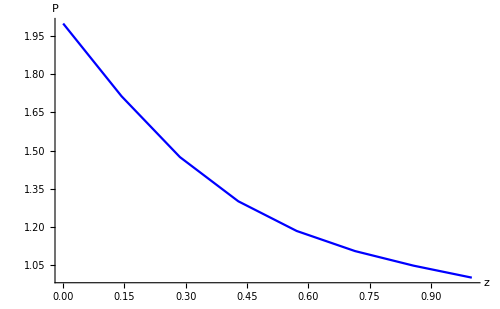

```mathematica
(*3d graph*)
listPlotDiagram = ListPointPlot3D[diagram3DGauss,
PlotStyle->PointSize[0.02],
ViewPoint->{-0.790,3.054,0.947},
PlotRange->All,
AxesLabel->{Style["z",16,
Black,Italic,FontFamily->"Times"],
Style["s",16,Italic,Black,FontFamily->"Times"],
Style["P",16,Black,Italic,FontFamily->"Times"]
},
AxesStyle->Directive[Black,14,Arrowheads[{0.0,0.03}],FontFamily->"Times"],
AxesStyle->Thick,
ImageSize->500,
Lighting->{{"Ambient", LightBlue}}];

(*surface*)
surface=Plot3D[1.0+0.2*s,{z,0.0,borderLength},{s,0.0,borderLength},
AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],
Style["s",16,Italic,Black,FontFamily->"Times"]
},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,
Background->White,
BoundaryStyle->Thick,
Filling->Bottom,
ImageSize->500,
FillingStyle-> LightBlue,
Lighting->{{"Ambient", LightBlue}}, ViewPoint->{3.07559,0.7744956,0.888102}];

(*axes labels for simple search rotation*)
axesOrigin1 = Graphics3D[{PointSize[0.05],
Point[{0,0,0},VertexColors->Red]}];
axesOrigin2 = Graphics3D[{PointSize[0.05],
Point[{0.02,0,0},VertexColors->Blue]}];
axesOrigin3 = Graphics3D[{PointSize[0.05],
Point[{0,0.02,0},VertexColors->Green]}];

(*proection*)
colomn =matrixSize/2+1;
graphT2 = Table[{0,0},{i,1,matrixSize}];
For[i=1,i≤matrixSize,i++,{
graphT2[[i]][[1]]=diagram3DGauss[[i]][[colomn]][[1]];
graphT2[[i]][[2]]=diagram3DGauss[[i]][[colomn]][[3]];
}];
proec = ListLinePlot[graphT2,
PlotRange->All,
GridLines->Full,
ImageSize->500,
PlotStyle->{Blue},
AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],Style["P",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,
PlotStyle->{Darker[Red,0.4],Thick}];
Show[listPlotDiagram]
Show[surface]
Show[proec,
PlotRange->All]
```

```mathematica
Plot3D[1+2*x+3*y+4*x*y,{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
rect = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
```

```mathematica
hLinear = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
```

```mathematica
Norm[rect-hLinear,Infinity]
```

0.

```mathematica
const = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
```

```mathematica
Norm[hLinear-const,Infinity]
```

0.

```mathematica
Norm[rect-const,Infinity]
```

0.